# korrekt n-Dimensional Fourier-Integrieren

```mathematica
(* CHECK: Nehme die gFraktur-Funktion *)
(* CHECK: Karbstein-Formel *)
gFraktur[r_] = 1/Pi^2 * l / (r^2 + l^2)^2;
Assuming[{r,p,l}∈Reals ∧l>0∧p>0,
2 Pi I / p * Integrate[r * gFraktur[r] * (Exp[-I p r] - Exp[+I p r]),{r,0,∞}]]
```

ⅇ^(-l p)

```mathematica
(* CHECK BESTANDEN!! *)
```

## h(r)-Modell in n Dim

```mathematica
(* Ausintegration der Winkel beim n-Dim-Fourierintegral *)
Dh[r_] = D[1/(1+(l/r)^2),r];
DhN[r_,n_] = D[1/(1+(l/r)^(2+n)),r];
```

```mathematica
(* n=0: Keine Extradimension, ein Winkel. *)
(* n=0: Möglichkeit A: Karbstein-Formel verwenden *)
Assuming[{r,p,l}∈Reals ∧l>0∧p>0,
2 Pi I / p * Integrate[r * Dh[r] * (Exp[-I p r] - Exp[+I p r]),{r,0,∞}]]//FullSimplify
```

(4 l π^(3/2) MeijerG[{{-1/2},{}},{{1/2,1/2},{0}},(l^2 p^2)/4])/p

```mathematica
(* n=0: Möglichkeit B: Nachintegration des Winkel cos(Subscript[θ, 1]) *)
Assuming[{r,c1,p,l}∈Reals∧l>0∧p>0,
Integrate[ r^2 * Dh[r] * Exp[I*p*r*c1], {r,0,∞},{c1,-1,1}]]
```

(2 l √π MeijerG[{{-1/2},{}},{{1/2,1/2},{0}},(l^2 p^2)/4])/p

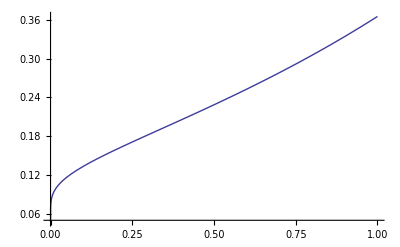

```mathematica
(* PLOTTE mal das 1d-Ergebnis *)
A[p_]=((4 l π^(3/2) MeijerG[{{-1/2},{}},{{1/2,1/2},{0}},(l^2 p^2)/4])/p) ^(-1/2) /.{l-> 1};
Plot[Re[A[p]], {p,0,1}]
```

```mathematica
(* n=1 Extradimension: Karbstein geht *)
Assuming[{r,c1,p,l}∈Reals∧l>0∧p>0,
I/p  * Integrate[ r^2 * D[1/(1+(l/r)^(2+1)),r] *( Exp[-I*p*r] - Exp[+I*p*r]),
{r,0,∞}]]
```

1/p 2 l^2 √(3/π) MeijerG[{{-1/3,1/6},{}},{{1/6,1/6,1/2,2/3,5/6},{0,1/3,2/3}},(l^6 p^6)/46656]

```mathematica
(* n=2 Extradimension: EIN Winkel (Cosinus!) *)
Assuming[{r,c1,p,l}∈Reals∧l>0∧p>0,
I/p  * Integrate[ r^2 * D[1/(1+(l/r)^(2+1)),r] *( Exp[-I*p*r] - Exp[+I*p*r]),
{r,0,∞}]]
```

(2 l^3 √(2 π) MeijerG[{{-3/4},{}},{{1/4,1/4,3/4},{0,1/2}},(l^4 p^4)/256])/p

```mathematica
(* n=0..4 extradimension: Karbstein *)
Table[
Assuming[{r,c1,p,l}∈Reals∧l>0∧p>0,
I/p  * Integrate[ r^(n+1) * D[1/(1+(l/r)^(2+n)),r] *( Exp[-I*p*r] - Exp[+I*p*r]),
{r,0,∞}]],
{n,{0,1,2,3,4}}]
```

{(2 l √π MeijerG[{{-1/2},{}},{{1/2,1/2},{0}},(l^2 p^2)/4])/p,1/p 2 l^2 √(3/π) MeijerG[{{-1/3,1/6},{}},{{1/6,1/6,1/2,2/3,5/6},{0,1/3,2/3}},(l^6 p^6)/46656],(2 l^3 √(2 π) MeijerG[{{-3/4},{}},{{1/4,1/4,3/4},{0,1/2}},(l^4 p^4)/256])/p,1/p 2 l^4 √(5/π) MeijerG[{{-2/5,1/10},{}},{{1/10,1/10,3/10,1/2,3/5,7/10,9/10},{0,1/5,2/5,3/5,4/5}},(l^10 p^10)/10000000000],1/p 2 l^5 √(3 π) MeijerG[{{-5/6},{}},{{1/6,1/6,1/2,5/6},{0,1/3,2/3}},(l^6 p^6)/46656]}

```mathematica
(* Was ist, wenn man Karbstein zum Residuensatz ausformuliert? *)
Grid[Join @@ { {Style[#,{Blue, Bold, 12}]& /@
{"n", "Lösung für A^-2, in Vielfachen von p (!!) also *p"}},
Table[{n,
Assuming[{r,p,l}∈Reals∧l>0∧p>0,
(-1)^(n+1) *I (* /p *)  * Integrate[ r^(n+1) *
(HeavisideTheta[-r]*DhN[-r,n]+HeavisideTheta[r]*DhN[r,n]) * Exp[-I*p*r],
{r,-∞,∞}]]},
{n,{0,1,2,3,4,5}}]
},
Frame -> All, Alignment-> {Left,Left}]
(* Mathematica Darstellung der MeijerG-Funktion:
MeijerG[{{a1,...,an},{an+1,...,ap}},{{b1,...,bm},{bm+1,...,bq}},z] *)
```

n | Lösung für A^-2, in Vielfachen von p (!!) also *p
0 | -2 l √π MeijerG[{{-1/2},{}},{{1/2,1/2},{0}},(l^2 p^2)/4]
1 | 2 ⅈ l^2 √(3/π) MeijerG[{{-1/3},{}},{{0,1/6,1/3,2/3,2/3},{1/2,5/6}},(l^6 p^6)/46656]
2 | -2 l^3 √(2 π) MeijerG[{{-3/4},{}},{{1/4,1/4,3/4},{0,1/2}},(l^4 p^4)/256]
3 | 2 ⅈ l^4 √(5/π) MeijerG[{{-2/5},{}},{{0,1/10,1/5,2/5,3/5,3/5,4/5},{3/10,1/2,7/10,9/10}},(l^10 p^10)/10000000000]
4 | -2 l^5 √(3 π) MeijerG[{{-5/6},{}},{{1/6,1/6,1/2,5/6},{0,1/3,2/3}},(l^6 p^6)/46656]
5 | 2 ⅈ l^6 √(7/π) MeijerG[{{-3/7},{}},{{0,1/14,1/7,2/7,3/7,4/7,4/7,5/7,6/7},{3/14,5/14,1/2,9/14,11/14,13/14}},(l^14 p^14)/11112006825558016]

## h_α-Modell in n Dimensionen

```mathematica
(* Und nun nochmal für das hAlpha-Modell. *)
DhAlph[r_,n_] = D[1/(1+(l/r)^α / 2)^((3+n)/α),r]
```

(l (3+n) (1+1/2 (l/r)^α)^(-1-(3+n)/α) (l/r)^(-1+α))/(2 r^2)

```mathematica
(* Dieses Integral wird quasi nicht fertig (>20min...). *)
Table[{n,
Assuming[{r,α,p,l}∈Reals∧α>0∧l>0∧p>0,
(-1)^(n+1) *I /p  * Integrate[ r^(n+1) *
(HeavisideTheta[-r]*DhAlph[-r,n]+HeavisideTheta[r]*DhAlph[r,n]) * Exp[-I*p*r],
{r,-∞,∞}]]},
{n,{0}}]
```

$Aborted

```mathematica
(* Probieren wir es nochmal mit Subscript[h, α]'(z): *)
DhAlphZ[z_,n_] = D[1/(1+(1/z)^α / 2)^((3+n)/α), z] // FullSimplify;
```

```mathematica
Table[{n,
Assuming[{z,α,p,l}∈Reals∧α>0∧p>0,
(-1)^(n+1) *I /p  * Integrate[z^(n+1) *
(HeavisideTheta[-z]*DhAlphZ[-z,n]+HeavisideTheta[z]*DhAlphZ[z,n]) * Exp[-I*p*l*z],
{z,-∞,∞}]]},
},
{n,{0}}]
```